```mathematica
N[Sqrt[(Cos[Pi/4])^2/((Cos[Pi/4])^2-(Sin[ Pi/5])^2)]]
```

1.79891

```mathematica
Cos[ 2Pi/5],Sin[ 2Pi/5]
```

```mathematica
Lr={{1,0,0},{0,1,0},{0,0,-1}};
```

```mathematica
MatrixForm[%]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)

```mathematica
refl3C[a_][x_]:=(a.Lr.a)x-2(x.Lr.a)a
de2a3C[{x_,y_}]:={x,y,1}
de3a2C[{x_,y_,z_}]:=(1/z){x,y}
ref2C[a_][x_]:=de3a2C[refl3C[de2a3C[a]][de2a3C[x]]]
```

```mathematica
aCiclo[l_]:=Append[l,First[l]]
```

```mathematica
de2a3CLr[{x_,y_}]:={x,y,-1}
```

```mathematica
linePara[t_][{v_,u_}]:=Expand[(1-t)v+t u]
vert[listaVert_][i_]:=listaVert[[i]]
dibujaPoligKlein[vDX_][aristasDX_]:=Graphics[Map[Line,vert[vDX][#]&/@aristasDX,{1}],PlotRange->All,Axes->False]
vert[listaVert_][i_]:=listaVert[[i]]
kleinAPoinc[x_]:=((1-Sqrt[1-x.x])/x.x)x
linePara[t_][{v_,u_}]:=Expand[(1-t)v+t u]
dibujaPoligPoincare[vDX_][aristasDX_]:=ParametricPlot[kleinAPoinc/@Map[linePara[t],vert[vDX][#]&/@aristasDX,{1}],{t,0,1},Axes->False,PlotStyle->{Black}]
```

```mathematica
N[Sqrt[(Cos[Pi/3])^2/((Cos[Pi/3])^2-(Sin[ Pi/9])^2)]]
```

1.37091

## Triangulo

```mathematica
vTD=1.3709067224183475{Cos[# 2Pi/9],Sin[# 2Pi/9]}&/@{0,1,2,3,4,5,6,7,8};
```

```mathematica
vTkl=de3a2C[#]&/@Apply[Cross,Partition[de2a3CLr/@aCiclo[vTD],2,1],{1}];
```

```mathematica
aristasT={{1,2},{2,3},{3,4},{4,1}};
```

```mathematica
vT=de3a2C[#]&/@Apply[Cross,Partition[de2a3CLr/@aCiclo[vTD],2,1],{1}];
```

```mathematica
verT[{}]=N[vTkl];
verTD[{}]=N[vTD];
verT[xL_]:=verT[xL]=Chop[
ref2C[verTD[Most[xL]][[Last[xL]]]]/@verT[Most[xL]]];
verTD[xL_]:=verTD[xL]=Chop[
ref2C[verTD[Most[xL]][[Last[xL]]]]/@verTD[Most[xL]]];
```

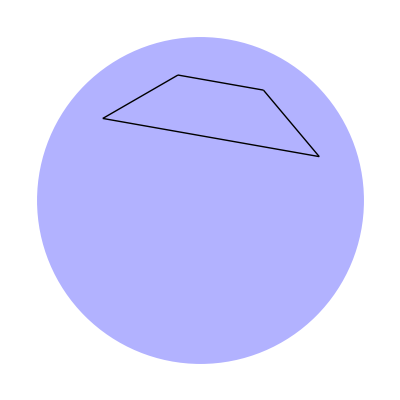

```mathematica
capaT[k][0]=Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaPoligKlein[vTkl][aristasT]]
```

## Funciones

```mathematica
Lr={{1,0,0},{0,1,0},{0,0,-1}};
```

```mathematica
MatrixForm[%]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)

```mathematica
refl3C[a_][x_]:=(a.Lr.a)x-2(x.Lr.a)a
de2a3C[{x_,y_}]:={x,y,1}
de3a2C[{x_,y_,z_}]:=(1/z){x,y}
ref2C[a_][x_]:=de3a2C[refl3C[de2a3C[a]][de2a3C[x]]]
```

```mathematica
aCiclo[l_]:=Append[l,First[l]]
```

```mathematica
linePara[t_][{v_,u_}]:=Expand[(1-t)v+t u]
vert[listaVert_][i_]:=listaVert[[i]];

dibujaPoligKlein[vDX_][aristasDX_]:=Graphics[Map[Line,vert[vDX][#]&/@aristasDX,{1}],PlotRange->All,Axes->False];

kleinAPoinc[x_]:=((1-Sqrt[1-x.x])/x.x)x;

dibujaPoligPoincare[vDX_][aristasDX_]:=ParametricPlot[kleinAPoinc/@Map[linePara[t],vert[vDX][#]&/@aristasDX,{1}],{t,0,1},Axes->False,PlotStyle->{Black}]
```

```mathematica
lineParaP[t_][{v_,u_}]:=Simplify[Expand[kleinAPoinc[linePara[t][{v,u}]]]]
```

```mathematica
dibujaLineasPoincare[listaPares_][color_][g_]:=ParametricPlot[lineParaP[t]/@listaPares,{t,0,1},Axes->False,PlotStyle->{color,Thickness[g]}]
```

## Nonagono

```mathematica
N[Sqrt[(Cos[Pi/9])^2/((Cos[Pi/9])^2-(Sin[ Pi/3])^2)]]
```

2.57646

```mathematica
vTD=2.576461861684634{Cos[# 2Pi/3],Sin[# 2Pi/3]}&/@{0,1,2};
```

```mathematica
vTkl=de3a2C[#]&/@Apply[Cross,Partition[de2a3CLr/@aCiclo[vTD],2,1],{1}];
```

```mathematica
aristasT={{1,2},{2,3},{3,1}};
```

```mathematica
vT=de3a2C[#]&/@Apply[Cross,Partition[de2a3CLr/@aCiclo[vTD],2,1],{1}];
```

```mathematica
verT[{}]=N[vTkl];
verTD[{}]=N[vTD];
verT[xL_]:=verT[xL]=Chop[
ref2C[verTD[Most[xL]][[Last[xL]]]]/@verT[Most[xL]]];
verTD[xL_]:=verTD[xL]=Chop[
ref2C[verTD[Most[xL]][[Last[xL]]]]/@verTD[Most[xL]]];
```

```mathematica
extiende[xL_]:=Append[xL,#]&/@Complement[{1,2,3},{Last[xL]}]
```

```mathematica
extiende[{1,2,1}]
```

{{1,2,1,2},{1,2,1,3}}

```mathematica
capaCombC[0]={{}};
capaCombC[1]={{1},{2},{3}};
```

```mathematica
capaCombC[n_]:=capaCombC[n]=Join@@(extiende/@capaCombC[n-1])
```

```mathematica
capaCombC[3];
```

## Dibujos

```mathematica
refComb[{}][x_]:=x;
refComb[i_Integer][x_]:=ref2C[vTD[[i]]][x];
refComb[xL_][x_]:=refComb[Most[xL]][refComb[Last[xL]][x]]
```

```mathematica
nonagono[xL_]:=refComb[xL]/@vT
```

```mathematica
tri0=Partition[aCiclo[vT],2,1]
```

{{{0.388129,0.672259},{-0.776258,0.}},{{-0.776258,0.},{0.388129,-0.672259}},{{0.388129,-0.672259},{0.388129,0.672259}}}

```mathematica
tria0[xL_]:=Map[refComb[xL],tri0,{2}]
```

```mathematica
non0={{{0,0},refComb[1][{0,0}]},{{0,0},refComb[2][{0,0}]},{{0,0},refComb[3][{0,0}]}}
```

{{{0,0},{0.674629,0.}},{{0,0},{-0.337315,0.584246}},{{0,0},{-0.337315,-0.584246}}}

```mathematica
non[xL_]:=Map[refComb[xL],non0,{2}]
```

```mathematica
non[{1,2,3}]
```

{{{0.937797,0.267854},{0.933917,0.339918}},{{0.937797,0.267854},{0.978655,0.149909}},{{0.937797,0.267854},{0.824352,0.351318}}}

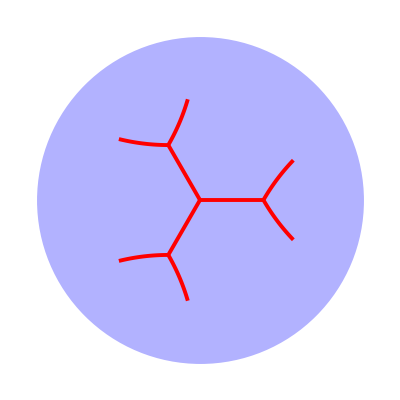

```mathematica
Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaLineasPoincare[non[#]][Red][0.007]&/@capaCombC[1]]
```

```mathematica
finales[n_]:=repite[n]/@Permutations[Range[3],{2}]
repite[1][xL_]:=xL
repite[n_][xL_]:=Join[repite[n-1][xL],xL]
```

```mathematica
finalesX[n_]:=Join[finales[n],Most/@finales[n]]
```

```mathematica
finalesX[2]
```

{{1,2,1,2},{1,3,1,3},{2,1,2,1},{2,3,2,3},{3,1,3,1},{3,2,3,2},{1,2,1},{1,3,1},{2,1,2},{2,3,2},{3,1,3},{3,2,3}}

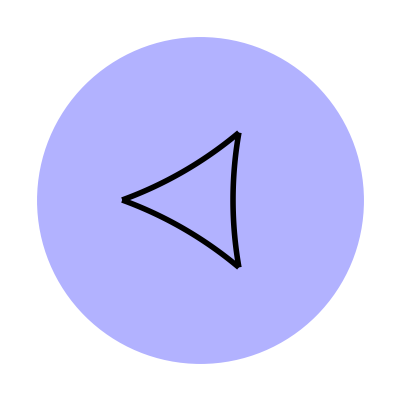

```mathematica
Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaLineasPoincare[tria0[#]][Black][0.01]&/@capaCombC[0]]
```

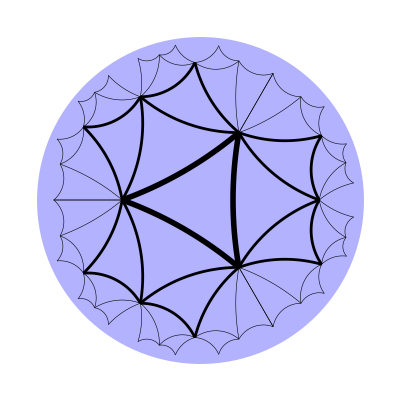

```mathematica
Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaLineasPoincare[tria0[#]][Black][0.01]&/@capaCombC[0],dibujaLineasPoincare[tria0[#]][Black][0.005]&/@capaCombC[2],dibujaLineasPoincare[tria0[#]][Black][0.001]&/@capaCombC[4],dibujaLineasPoincare[tria0[#]][Black][0.00025]&/@finalesX[4]]
```

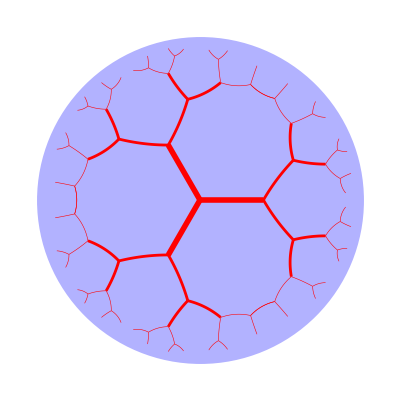

```mathematica
Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaLineasPoincare[non[#]][Red][0.01]&/@capaCombC[0],dibujaLineasPoincare[non[#]][Red][0.005]&/@capaCombC[2],dibujaLineasPoincare[non[#]][Red][0.001]&/@capaCombC[4],dibujaLineasPoincare[non[#]][Red][0.00025]&/@finalesX[4]]
```

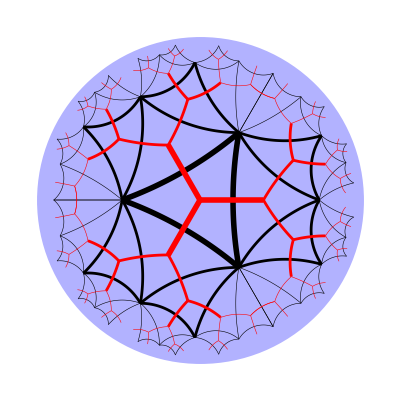

```mathematica
Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaLineasPoincare[tria0[#]][Black][0.01]&/@capaCombC[0],dibujaLineasPoincare[tria0[#]][Black][0.005]&/@capaCombC[2],dibujaLineasPoincare[tria0[#]][Black][0.001]&/@capaCombC[4],dibujaLineasPoincare[tria0[#]][Black][0.00025]&/@finalesX[4],dibujaLineasPoincare[non[#]][Red][0.01]&/@capaCombC[0],dibujaLineasPoincare[non[#]][Red][0.005]&/@capaCombC[2],dibujaLineasPoincare[non[#]][Red][0.001]&/@capaCombC[4],dibujaLineasPoincare[non[#]][Red][0.00025]&/@finalesX[4]]
```

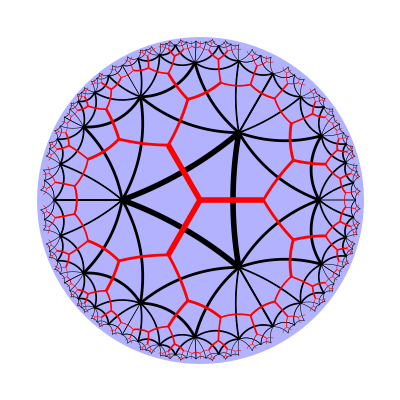

```mathematica
Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaLineasPoincare[tria0[#]][Black][0.01]&/@capaCombC[0],dibujaLineasPoincare[tria0[#]][Black][0.005]&/@capaCombC[2],dibujaLineasPoincare[tria0[#]][Black][0.003]&/@capaCombC[4],dibujaLineasPoincare[tria0[#]][Black][0.001]&/@capaCombC[6],dibujaLineasPoincare[tria0[#]][Black][0.00025]&/@finalesX[6],
dibujaLineasPoincare[non[#]][Red][0.01]&/@capaCombC[0],dibujaLineasPoincare[non[#]][Red][0.005]&/@capaCombC[2],dibujaLineasPoincare[non[#]][Red][0.003]&/@capaCombC[4],dibujaLineasPoincare[non[#]][Red][0.001]&/@capaCombC[6],dibujaLineasPoincare[non[#]][Red][0.00025]&/@finalesX[6]]
```

```mathematica
Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaLineasPoincare[tria0[#]][Black][0.0065]&/@capaCombC[0],dibujaLineasPoincare[tria0[#]][Black][0.005]&/@capaCombC[2],dibujaLineasPoincare[tria0[#]][Black][0.003]&/@capaCombC[4],dibujaLineasPoincare[tria0[#]][Black][0.002]&/@capaCombC[6],dibujaLineasPoincare[tria0[#]][Black][0.001]&/@capaCombC[8],dibujaLineasPoincare[tria0[#]][Black][0.00025]&/@finalesX[8],
dibujaLineasPoincare[non[#]][Black][0.0065]&/@capaCombC[0],dibujaLineasPoincare[non[#]][Black][0.005]&/@capaCombC[2],dibujaLineasPoincare[non[#]][Black][0.003]&/@capaCombC[4],dibujaLineasPoincare[non[#]][Black][0.002]&/@capaCombC[6],dibujaLineasPoincare[non[#]][Black][0.001]&/@capaCombC[8],dibujaLineasPoincare[non[#]][Black][0.00025]&/@finalesX[8]]
```

-Graphics-

```mathematica
Show[Graphics[{Blue,Opacity[.3],Disk[{0,0},1]}],dibujaLineasPoincare[tria0[#]][Black][0.01]&/@capaCombC[0],dibujaLineasPoincare[tria0[#]][Black][0.005]&/@capaCombC[2],dibujaLineasPoincare[tria0[#]][Black][0.003]&/@capaCombC[4],dibujaLineasPoincare[tria0[#]][Black][0.001]&/@capaCombC[6],dibujaLineasPoincare[tria0[#]][Black][0.001]&/@capaCombC[8],dibujaLineasPoincare[tria0[#]][Black][0.00025]&/@finalesX[8]]
```

-Graphics-